```mathematica
(* Helper Functions *)
t1d[params_] := Transpose[{params}] 
listProduct[l_] := Product[l[[i]],{i,1,Length[l]}]
grabElements[l_,e_] := Map[l[[#]]&,e] 
generateFluxCoefficients[GE_,S_] :=Map[listProduct[grabElements[GE,Position[#,_?Negative][[All,1]]]]&,Transpose[S]]
solveForParameters[v_,coeff_]  := v / coeff (*MapThread[#1/#2&,{v,coeff}]*)
solveForFluxesConstrained[SS_,fluxes_,S_,x1_,x2_,x3_,error_] := fluxes /.NMinimize[{Norm[fluxes[[-3;;-1]]-{x3,x2,x1}],Norm[SS - S.t1d[fluxes]] <=error,fluxes ≥ 0.001},fluxes,AccuracyGoal->2][[2]];
solveForFluxes[SS_,fluxes_,S_,error_] := fluxes /.NMaximize[{fluxes[[RandomInteger[{1,Length[fluxes]}]]],Norm[SS-S.t1d[fluxes]] == 0,fluxes >= 0.001,fluxes ≤ 300},fluxes,AccuracyGoal->2,MaxIterations -> 100][[2]];
FVA[SS_,fluxes_,S_] := {
Map[NMinimize[
{#,fluxes>=.001 ,fluxes <= 300,Norm[SS-S.t1d[fluxes]] == 0},fluxes,MaxIterations -> 100,AccuracyGoal->2]&,fluxes][[All,1]],
Map[NMaximize[
{#,fluxes>=.001 ,fluxes <= 300,Norm[SS-S.t1d[fluxes]] == 0},fluxes,MaxIterations -> 100,AccuracyGoal->2]&,fluxes][[All,1]]};
getTermFromReaction[SCol_,species_,rateConstant_,fluxes_] := 
Module[{term=rateConstant},
Map[(term = term *(species[[#]])^Abs[SCol[[#]]])&,Position[SCol,_?Negative][[All,1]]];
If[(term - rateConstant) < .00001,term = fluxes];
{Map[{SCol[[#]],species[[#]]}&,Range[Length[SCol]]],
term}
]
addTermToReaction[reactionList_,species_,term_,toReactions_] := 
Module[{temp},
temp = reactionList;
Map[
temp[[Position[species,#[[2]]][[1,1]]]] += #[[1]]*term &,
toReactions];
temp]
generateExpressions[S_,species_,IC_,var_,rateConstants_,fluxes_] := 
Module[{reactionList = ConstantArray[0,Length[species]],allReactions},
allReactions = MapThread[getTermFromReaction[#1,species,#2,#3]&,{Transpose[S],rateConstants,fluxes}];
allReactions = Total[Map[addTermToReaction[reactionList,species,#[[2]],#[[1]]]&,allReactions]];
Join[
MapThread[#2 == #1&,{allReactions /. Map[# -> #[var]&,species],species /. Map[# -> #'[var]&,species]}],
MapThread[#2 == #1&,{IC,species /. Map[# -> #[0]&,species]}]
]
]
```

For the given toy reaction network:
a ->b
b -> c + d
b + d -> g
g + c -> a 
f -> d + e
d + e -> f
e + a -> g
a + d -> e
aE->a
->aE (input glucose)
c->cE (measured)
g->gE (measured)

```mathematica
(*Reaction Network*)
S = {{1,-1,0,0,0,-1,-1,1,0,0,0},{-1,1,-1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,-1,0},{0,0,1,-1,1,0,-1,0,0,0,0},{0,0,0,-1,1,-1,1,0,0,0,0},{0,0,0,1,-1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,-1},{0,0,0,0,0,0,0,-1,1,0,0},{0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,1}};
S =S[[All,{2,3,4,6,7,8,9,10,11}]];
S = Transpose[Insert[Transpose[S],{0,-1,0,-1,0,0,1,0,0,0},2]];
S = Transpose[Insert[Transpose[S],{1,0,-1,0,0,0,-1,0,0,0},3]];
S = Transpose[Insert[Transpose[S],{0,0,0,1,1,-1,0,0,0,0},4]];
SPrime = Transpose[Insert[Transpose[S],{0,0,0,0,0,0,0,0,-1,0},1]];
SPrime = Transpose[Insert[Transpose[SPrime],{0,0,0,0,0,0,0,0,0,-1},1]];
Clear[v1,v2,v3,v4,v5,v6,v7,v8,v9,v10,v11,v12,a,b,c,d,e,f,g,aE,cE,gE]
fluxes = {v1,v2,v3,v4,v5,v6,v7,v8,v9,v10,v11,v12};
fluxesPrime = {v1,v2,v3,v4,v5,v6,v7,v8,v9,v10,v11,v12,v13,v14};
MatrixRank[S]
Length[fluxes]
species = {a,b,c,d,e,f,g,aE,cE,gE};
SS  = ConstantArray[0,{Length[S],1}];
error = .1;
tmax =1000;
bolus = 100;

Print[SS//MatrixForm,"=",SPrime//MatrixForm,t1d[fluxesPrime] //MatrixForm]
```

9

12

(0
0
0
0
0
0
0
0
0
0)=(0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | -1 | 0 | 1 | 1 | -1 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)(v1
v2
v3
v4
v5
v6
v7
v8
v9
v10
v11
v12
v13
v14)

```mathematica
(*Find the maximum flux for each reaction individually *)
{fluxMinimum,fluxMaximum} =FVA[SS,fluxesPrime,SPrime];
Print[fluxMinimum // MatrixForm,"≤",t1d[fluxesPrime] // MatrixForm, "≤" ,fluxMaximum // MatrixForm]
```

(0.001
0.001
0.00299903
0.001
0.001
0.0010008
0.00199983
0.001
0.00100561
0.001007
0.00399821
0.00400001
0.001
0.001)≤(v1
v2
v3
v4
v5
v6
v7
v8
v9
v10
v11
v12
v13
v14)≤(149.992
147.309
300.
149.999
160.987
300.
196.716
300.
149.999
150.008
300.
300.
149.996
145.449)

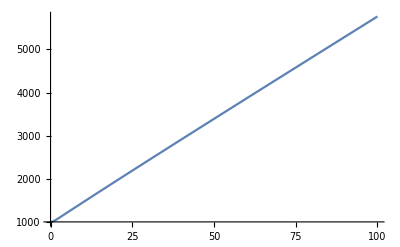
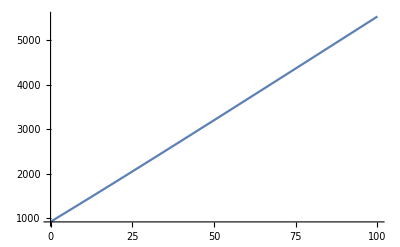

{{47.0238},{47.0238}}

```mathematica
(*Measured flux values for WT*)
x1 = 1;
x2 = 1;
x3 = 2;
 fluxValuesWT = solveForFluxesConstrained[SS,fluxesPrime,SPrime,x1,x2,x3,error];
(*Print[SPrime.fluxValuesWT]*)
fluxValuesWT = fluxValuesWT[[3;;-1]];
(*Print[t1d[fluxes] // MatrixForm,"=",t1d[fluxValuesWT] //MatrixForm] *)
GEWT = RandomReal[{0,1},Length[S]];
fluxCoefficientsWT = fluxValuesWT /generateFluxCoefficients[GEWT,S];
translationCoeff = RandomReal[{0,1},Length[species]];
baseLineKs =fluxValuesWT /generateFluxCoefficients[GEWT*translationCoeff,S];
expressions = generateExpressions[S,species,ConstantArray[0,Length[species]],t,baseLineKs,fluxValuesWT];
sol =NDSolve[expressions,species,{t,0,tmax}];
(*Map[Plot[Evaluate[#[t] /. sol],{t,0,tmax},PlotRange -> All]&,species]*)
SSConcentrationsWT = Map[(Evaluate[#[tmax] /. sol])[[1]]&,species];
(*SSConcentrationsWT[[-3]]+=bolus;*)
fluxValuesWT[[10]] += bolus;
expressions = generateExpressions[S,species,SSConcentrationsM,t,baseLineKs*ratioKs,(*0**)fluxValuesWT];
sol =NDSolve[expressions,species,{t,0,tmax}];
Map[Plot[Evaluate[#[t] /. sol],{t,0,tmax/10},PlotRange -> All]&,{cE,gE}]
Map[N[Evaluate[(#[tmax]-#[tmax-50])/50 /. sol]]&,{cE,gE}]
```

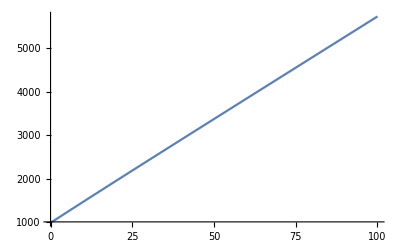
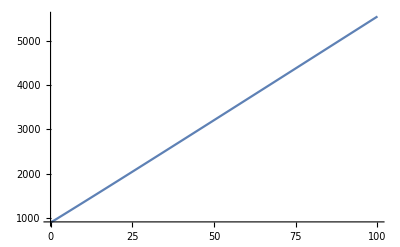

{{46.9916},{46.9916}}

```mathematica
x1 = .001;
x2 = 2;
x3 = 2;
 fluxValuesM = solveForFluxesConstrained[SS,fluxesPrime,SPrime,x1,x2,x3,error];
(*Print[SPrime.fluxValuesM];*)
fluxValuesM = fluxValuesM[[3;;-1]];
GEM = RandomReal[{0,1},Length[S]];
fluxCoefficientsM = fluxValuesM /generateFluxCoefficients[GEM,S];
ratioKs = fluxCoefficientsM/fluxCoefficientsWT;
(*Print["{K}_m/{K}_wt = ", ratioKs// MatrixForm]*)
expressions = generateExpressions[S,species,ConstantArray[0,Length[species]],t,baseLineKs*ratioKs,fluxValuesM];
sol =NDSolve[expressions,species,{t,0,tmax}];
(*Map[Plot[Evaluate[#[t] /. sol],{t,0,1000},PlotRange -> All]&,species]*)
SSConcentrationsM = Map[(Evaluate[#[tmax] /. sol])[[1]]&,species];
(*SSConcentrationsM[[-3]]+=bolus;*)
fluxValuesM[[10]] += bolus;
expressions = generateExpressions[S,species,SSConcentrationsM,t,baseLineKs*ratioKs,(*0**)fluxValuesM];
sol =NDSolve[expressions,species,{t,0,tmax}];
Map[Plot[Evaluate[#[t] /. sol],{t,0,tmax/10},PlotRange -> All]&,{cE,gE}]
Map[N[Evaluate[(#[tmax]-#[tmax-50])/50 /. sol]]&,{cE,gE}]
```